# Homework 4

Name: Eslam Muhammed Ahmed Zenhom

ID: 201700788

## Problem 1

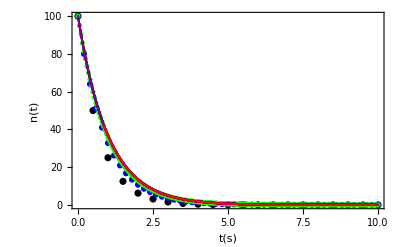

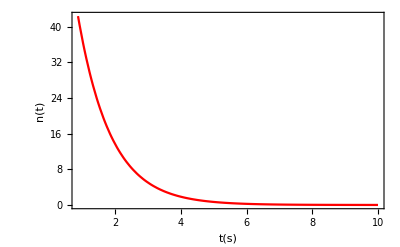

```mathematica
ClearAll["Global`*"];
 n[t_,n0_,τ_ ]:=n0 ⅇ^(-t/τ) (* Exact solution *)
tau =1.0;  tStart = 0.0;tMax = 10; n0 = 100;
dt = {0.5,0.2,0.05,0.001}; (* different time steps *)

ldt = Length[dt];
color = {Black,Blue,Green, Purple};
pList = Array[plot,ldt];

Do[ (* over the values of dt *)
tList = Range[tStart,tMax,dt[[ndt]]];
lt = Length[tList];
nt = Table[0,{i,lt}];
nt[[1]] = n0;
const = (1- dt[[ndt]]/tau);

 (* Calculation *)
Do[nt[[i]] = const nt[[i-1]],{i,2,lt}]; (* Euler method *)ntList = Table[{tList[[i]],nt[[i]]},{i,lt}];

(* Results *)
plot[ndt] = ListPlot[ntList,PlotStyle->color[[ndt]]];
,{ndt,ldt}];

p2 = Plot[n[t,n0,tau ],{t,tStart,tMax},PlotStyle->Red];
Show[{pList,p2},PlotRange->All,Frame -> True,FrameLabel->{Style[t[s],Large],Style[n[t],Large]},LabelStyle->20]
Show[{p2},PlotRange->All,Frame -> True,FrameLabel->{Style[t[s],Large],Style[n[t],Large]},LabelStyle->20]

(*The exact solution comes from DSolve[{n'[t]==-n[t]/τ,n[0]==1},n[t],t] *)
(*the purple line is almost above the red oneas the red one is the exact while the purple has a step of 0.001 and the pattern is clear as we decrease the step we find the curves converges to the red exact solution.*)
```

## Problem 2

{{q[t]→(ⅇ^-t (-1+ⅇ^t))/100000}}

{(ⅇ^-t (-1+ⅇ^t))/100000}

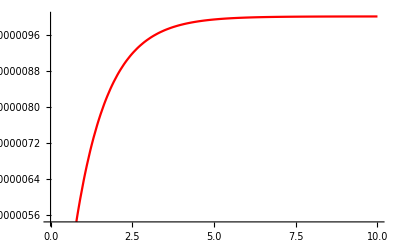

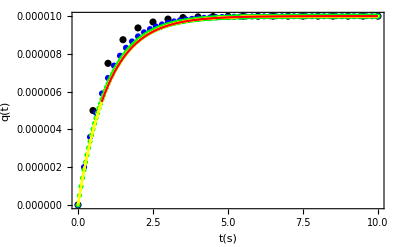

```mathematica
clearAll["Global`*"];
v=10;R=10^6; c=10^-6;
 sol=DSolve[{v==q'[t]*R+q[t]/c,q[0]==0},q[t],t](* Exact solution *)
n1 =q[t]/.sol
dt = {0.5,0.2,0.05,0.001}; (* different time steps *)

ldt = Length[dt];
color = {Black,Blue,Green, Yellow};
pList = Array[plot,ldt];

Do[ (* over the values of dt *)
tList = Range[tStart,tMax,dt[[qdt]]];
lt = Length[tList];
qt = Table[0,{i,lt}];
qt[[1]] = 0;
const = (1- dt[[qdt]]);

 (* Calculation *)
Do[qt[[i]] = const qt[[i-1]]+dt[[qdt]]*v/R,{i,2,lt}]; (* Euler method *)ntList = Table[{tList[[i]],qt[[i]]},{i,lt}];

(* Results *)
plot[qdt] = ListPlot[ntList,PlotStyle->color[[qdt]]];
,{qdt,ldt}];

p2 = Plot[n1,{t,tStart,tMax},PlotStyle->Red]
Show[{pList,p2},PlotRange->All,Frame -> True,FrameLabel->{Style[t[s],Large],Style[q[t],Large]},LabelStyle->20]

(*The exact solution comes from DSolve[{n'[t]==-n[t]/τ,n[0]==1},n[t],t] *)
(*For part b as you can see I plotted for four values of Delta t and when the step decreases to the lowest one (0.001) the yellow graph it converges to the exact value in the red graph*)
```

## Problem 3

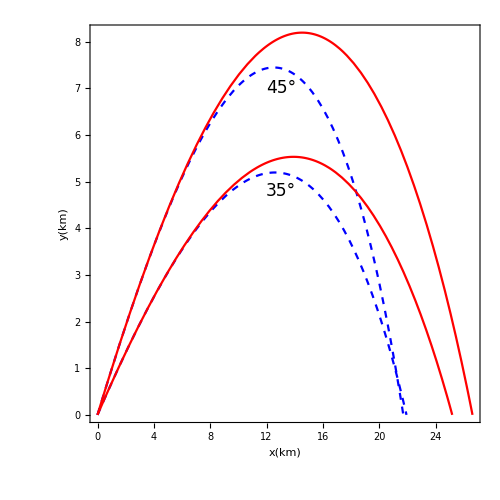

```mathematica
clearAll["Global`*"];
y0=10^4;
grav = 9.8; tmax = 1000; v0 = 700;B2m = 4.0 10^-5*ⅇ^(-y[t]/y0);  (* B2m = B2/m *)
θ=π/180.0 {35,45} ;lθ = Length[θ];
pWDrag = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
Do[vx0 = v0 Cos[θ[[nθ]]]; vy0 =v0 Sin[θ[[nθ]]];
solProj = NDSolve[{x'[t]==Subscript[v, x][t],Subscript[v, x]'[t]==-B2m Subscript[v, x][t]  √((Subscript[v, x][t])^2+(Subscript[v, y][t])^2),y'[t]==Subscript[v, y][t],Subscript[v, y]'[t]==-grav-B2m Subscript[v, y][t]  √((Subscript[v, x][t])^2+(Subscript[v, y][t])^2),x[0]==0.,y[0]==0.,Subscript[v, x][0]==vx0, Subscript[v, y][0]==vy0,WhenEvent[y[t]== 0.0,end = t]},{x,y},{t,tmax}];
pWDrag[[nθ]] =ParametricPlot[Evaluate[{x[t],y[t]}/1000./.solProj],{t,0,end},PlotStyle->Red],{nθ,lθ }]
pWDall = Show[pWDrag,PlotRange->All,Frame -> True,FrameLabel->{Style["x(km)",Large],Style["y(km)",Large]},LabelStyle->20,ImageSize->500 ,AspectRatio->1,Epilog->{ Inset[Style["35°",17] ,{13,4.8}],Inset[Style["45°",17],{13,7}]}];



C2m = 4.0 10^-5;
pWDrag2 = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
Do[vx0 = v0 Cos[θ[[nθ]]]; vy0 =v0 Sin[θ[[nθ]]];
solProj = NDSolve[{x'[t]==Subscript[v, x][t],Subscript[v, x]'[t]==-C2m Subscript[v, x][t]  √((Subscript[v, x][t])^2+(Subscript[v, y][t])^2),y'[t]==Subscript[v, y][t],Subscript[v, y]'[t]==-grav-C2m Subscript[v, y][t]  √((Subscript[v, x][t])^2+(Subscript[v, y][t])^2),x[0]==0.,y[0]==0.,Subscript[v, x][0]==vx0, Subscript[v, y][0]==vy0,WhenEvent[y[t]== 0.0,end = t]},{x,y},{t,tmax}];
pWDrag2[[nθ]] =ParametricPlot[Evaluate[{x[t],y[t]}/1000./.solProj],{t,0,end},PlotStyle->{Blue, Dashed}],{nθ,lθ }]
pWDall = Show[pWDrag2,pWDrag,PlotRange->All,Frame -> True,FrameLabel->{Style["x(km)",Large],Style["y(km)",Large]},LabelStyle->20,ImageSize->500 ,AspectRatio->1,Epilog->{ Inset[Style["35°",17] ,{13,4.8}],Inset[Style["45°",17],{13,7}]}]
```

## Problem 4

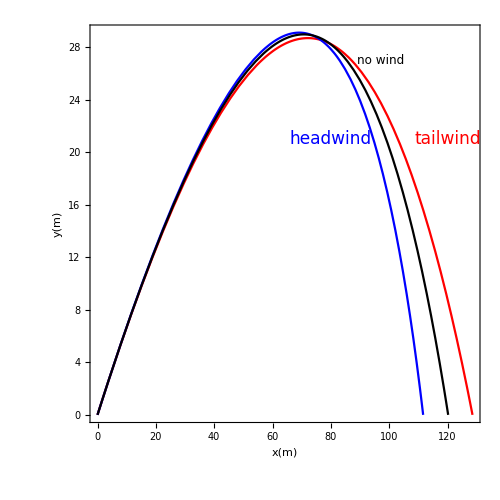

```mathematica
clearAll["Global`*"];
(*Tail wind*)

grav = 9.8; tmax = 1000; v0 = 49.1744;vwind=4.4704;
B2m =0.0039+0.0058/(1+Exp[(  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)-35)/5]);  (* B2m = B2/m *)
θ=π/180.0 {35} ;lθ = Length[θ];
pWDrag1 = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
Do[vx0 = v0 Cos[θ[[nθ]]]; vy0 =v0 Sin[θ[[nθ]]];
solProj = NDSolve[{x'[t]==Subscript[v, x][t],Subscript[v, x]'[t]==-B2m (Subscript[v, x][t]-vwind)*Abs[  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)],y'[t]==Subscript[v, y][t],Subscript[v, y]'[t]==-grav-B2m Subscript[v, y][t]  Abs[  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)],x[0]==0.,y[0]==0.,Subscript[v, x][0]==vx0, Subscript[v, y][0]==vy0,WhenEvent[y[t]== 0.0,end = t]},{x,y},{t,tmax}];
pWDrag1[[nθ]] =ParametricPlot[Evaluate[{x[t],y[t]}/.solProj],{t,0,end},PlotStyle->Red],{nθ,lθ }]



(*Head wind*)
grav = 9.8; tmax = 1000; v0 = 49.1744;vwind=-4.4704;
B2m =0.0039+0.0058/(1+Exp[(  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)-35)/5]);  (* B2m = B2/m *)
θ=π/180.0 {35} ;lθ = Length[θ];
pWDrag2 = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
Do[vx0 = v0 Cos[θ[[nθ]]]; vy0 =v0 Sin[θ[[nθ]]];
solProj = NDSolve[{x'[t]==Subscript[v, x][t],Subscript[v, x]'[t]==-B2m (Subscript[v, x][t]-vwind)*Abs[  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)],y'[t]==Subscript[v, y][t],Subscript[v, y]'[t]==-grav-B2m Subscript[v, y][t]  Abs[  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)],x[0]==0.,y[0]==0.,Subscript[v, x][0]==vx0, Subscript[v, y][0]==vy0,WhenEvent[y[t]== 0.0,end = t]},{x,y},{t,tmax}];
pWDrag2[[nθ]] =ParametricPlot[Evaluate[{x[t],y[t]}/.solProj],{t,0,end},PlotStyle->Blue],{nθ,lθ }]


(*No wind*)

grav = 9.8; tmax = 1000; v0 = 49.1744;vwind=0;
B2m =0.0039+0.0058/(1+Exp[(  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)-35)/5]);  (* B2m = B2/m *)
θ=π/180.0 {35} ;lθ = Length[θ];
pWDrag3 = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
Do[vx0 = v0 Cos[θ[[nθ]]]; vy0 =v0 Sin[θ[[nθ]]];
solProj = NDSolve[{x'[t]==Subscript[v, x][t],Subscript[v, x]'[t]==-B2m (Subscript[v, x][t]-vwind)*Abs[  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)],y'[t]==Subscript[v, y][t],Subscript[v, y]'[t]==-grav-B2m Subscript[v, y][t]  Abs[  (√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vwind)],x[0]==0.,y[0]==0.,Subscript[v, x][0]==vx0, Subscript[v, y][0]==vy0,WhenEvent[y[t]== 0.0,end = t]},{x,y},{t,tmax}];
pWDrag3[[nθ]] =ParametricPlot[Evaluate[{x[t],y[t]}/.solProj],{t,0,end},PlotStyle->Black],{nθ,lθ }]

pWDall = Show[pWDrag1,pWDrag2,pWDrag3,PlotRange->All,Frame -> True,FrameLabel->{Style["x(m)",Large],Style["y(m)",Large]},LabelStyle->20,ImageSize->500 ,AspectRatio->1,Epilog->{ Inset[Style["tailwind",17,Red] ,{120,21}], Inset[Style["headwind",17,Blue] ,{80,21}], Inset[Style["no wind",12,Black] ,{97,27}]}]
```